## Elliptical parametrizations

An elliptical mode can be written as the sum of two R/L circularly polarized modes. In terms of h ≡ h_+-i h_× , for a monochromatic mode this is
	h=1/(√2)(C_R e^(-i ω t)+C_L^*e^(i ω t))≡ 1/(√2)(A_R e^(-i (ω t-ϕ_R))+A_L e^(i (ω t-ϕ_L))) ,
where the C_(R/L)≡A_(R/L) e^(iϕ_(R/L)) are complex valued, but A_(R/L) are real. This is clearly written in terms of circular, R/L modes. We can rewrite this in terms of an ellipticity and related angles as follows:
	h=1/2 A [(1+ϵ) e^(-i (ω t-ϕ_R))+(1-ϵ) e^(i (ω t-ϕ_L))] ,
or, equivalently,
	h=A_[cosθ  cos(ω t-ϕ) - ϵ sinθ  sin(ω t-ϕ)] - i A [sinθ  cos(ω t-ϕ) + ϵ cosθ  sin(ω t-ϕ)] .
We could also replace {A,ϵ} with {Â=A √(1+ϵ^2),χ=arctan ϵ} to get another equivalent expression,
	h=OverHat[A_][cosχ cosθ  cos(ω t-ϕ) - sinχ  sinθ  sin(ω t-ϕ)] - i Â [cosχ sinθ  cos(ω t-ϕ) + sinχ  cosθ  sin(ω t-ϕ)] .
	
With some algebra, we can further show this to be equivalent to a template based on linear modes,
	h= ((A^+)_x cos ω t + (A^+)_y sin ω t)-i ((A^×)_x cos ω t + (A^×)_y sin ω t),
which is the same as
	h= A^+cos (ω t -φ^+) - i A^×cos (ω t -φ^×)e^(-t/τ_n).

### Coordinate transformations

The relevant coordinate transformations are as follows, suppressing the n index.

```mathematica
AepToAchi={
A->Ahat Cos[χ],
ϵ->Tan[χ]
};
AchiToAep={
Ahat->A Sqrt[1+ϵ^2],
χ->ArcTan[ϵ]
};
```

```mathematica
AepToCphi={
A-> (CR+CL)/Sqrt[2],
ϵ-> (CR -CL)/(CR+CL),
θ->(ϕL-ϕR)/2,
ϕ->(ϕL+ϕR)/2
};
CphiToAep={
CR->1/(√2) A (1+ϵ),
CL->1/(√2) A(1- ϵ),
ϕR->ϕ-θ,
ϕL->θ+ϕ
};
```

```mathematica
AphiToAxAy={
Ap->√(Apx^2+Apy^2),
Ac->√(Acx^2+Acy^2),
φp->ArcTan[Apx,Apy],
φc->ArcTan[Acx,Acy]
};
AxAyToAphi={
Apx->Ap Cos[φp],
Apy->Ap Sin[φp],
Acx->Ac Cos[φc],
Acy->Ac Sin[φc]
};

AxAyToCphi={
Apx->CR Cos[ϕR]+CL Cos[ϕL],
Apy->CR Sin[ϕR]+CL Sin[ϕL],
Acx->-CR Sin[ϕR]+CL Sin[ϕL],
Acy->CR Cos[ϕR]-CL Cos[ϕL]
};
```

Let’s find the inverse transformation for the last set:

```mathematica
(* Assuming[{Element[{Apx,Apy,Acx,Acy},Reals],CR>0,CL>0,0≤ϕR≤2π,0≤ϕL≤2π},
FullSimplify[Solve[Equal@@@Flatten[AxAyToCphi],{CR,CL,ϕR,ϕL}]]] *)
```

Unsurprisingly, there are multiple solutions. This shouldn’t matter for the Jacobian, so let’s take the one in the positive (x, y) quadrant for now

```mathematica
CphiToAxAy={
CR->1/2 √((Acy+Apx)^2+(Acx-Apy)^2),
CL->1/2 √((Acy-Apx)^2+(Acx+Apy)^2),
ϕR->ArcTan[Acy+Apx,-Acx+Apy],
ϕL->-ArcTan[-Acy+Apx,-Acx-Apy]
};
```

The corresponding transformation to (A, φ) is:

```mathematica
CphiToAphi=Assuming[{Ac>0,Ap>0,Element[{ϕp,ϕc},Reals]},FullSimplify[CphiToAxAy//.AxAyToAphi]]
```

{CR→1/2 √(Ac^2+Ap^2+2 Ac Ap Sin[φc-φp]),CL→1/2 √(Ac^2+Ap^2-2 Ac Ap Sin[φc-φp]),ϕR→ArcTan[Ap Cos[φp]+Ac Sin[φc],-Ac Cos[φc]+Ap Sin[φp]],ϕL→-ArcTan[Ap Cos[φp]-Ac Sin[φc],-Ac Cos[φc]-Ap Sin[φp]]}

We will also want to be able to go directly from linear quadratures to the elliptic parameterization (or vice-versa):

```mathematica
AepToAxAy =AepToCphi//.CphiToAxAy
```

{A→1/2 √((Acy+Apx)^2+(Acx-Apy)^2)+1/2 √((Acy-Apx)^2+(Acx+Apy)^2),ϵ→(1/2 √((Acy+Apx)^2+(Acx-Apy)^2)-1/2 √((Acy-Apx)^2+(Acx+Apy)^2))/(1/2 √((Acy+Apx)^2+(Acx-Apy)^2)+1/2 √((Acy-Apx)^2+(Acx+Apy)^2)),ϕ→1/2 (-ArcTan[-Acy+Apx,-Acx-Apy]+ArcTan[Acy+Apx,-Acx+Apy]),θ→1/2 (-ArcTan[-Acy+Apx,-Acx-Apy]-ArcTan[Acy+Apx,-Acx+Apy])}

```mathematica
FullSimplify[AepToAxAy //.AxAyToAphi]
```

{A→1/2 (√(Ac^2+Ap^2-2 Ac Ap Sin[φc-φp])+√(Ac^2+Ap^2+2 Ac Ap Sin[φc-φp])),ϵ→(Csc[φc-φp] (Ac^2+Ap^2-√(Ac^2+Ap^2-2 Ac Ap Sin[φc-φp]) √(Ac^2+Ap^2+2 Ac Ap Sin[φc-φp])))/(2 Ac Ap),ϕ→1/2 (-ArcTan[Ap Cos[φp]-Ac Sin[φc],-Ac Cos[φc]-Ap Sin[φp]]+ArcTan[Ap Cos[φp]+Ac Sin[φc],-Ac Cos[φc]+Ap Sin[φp]]),θ→1/2 (-ArcTan[Ap Cos[φp]-Ac Sin[φc],-Ac Cos[φc]-Ap Sin[φp]]-ArcTan[Ap Cos[φp]+Ac Sin[φc],-Ac Cos[φc]+Ap Sin[φp]])}

Compare to the “traditional” aligned parametrization, corresponding to the 22 mode of a nonprecessing system:
h= (1+cos^2 ι)A cos (ω t -φ)  - i 2cosι  A sin (ω t -φ)

```mathematica
ComplexExpand[FullSimplify[AepToAxAy //.AxAyToAphi //. {φp->φ,φc->φ+π/2,Ap->(1+cosι^2)A0,Ac->2cosι A0},{-1<=cosι<=1,A0>0,-Pi<φ<Pi}]]
```

{A→A0+A0 cosι^2,ϵ→(2 cosι)/(1+cosι^2),ϕ→φ,θ→0}

Finally, what is the transformation in terms of the true R and L amplitudes? By that I mean, the circular polarizations defined by h_R=1/(√2)(h_+- i h_×) and h_L=1/(√2)(h_++ i h_×).

```mathematica
TrigReduce[(hp - I hc)/Sqrt[2]//.{ hp->Ap Cos[ωt -φp], hc->Ac Sin[ωt -φc]}]
```

(Ap Cos[φp-ωt]+ⅈ Ac Sin[φc-ωt])/(√2)

```mathematica
Ar->(Ap Exp[I φp]-I Ac Exp[I φc])/Sqrt[2]
Al->(Ap Exp[I φp]+I Ac Exp[I φc])/Sqrt[2]
```

```mathematica
FullSimplify[CR^2 +CL^2 //.CphiToAep]
```

1/2 A^2 (1+ϵ^2)

```mathematica
FullSimplify[CR^2 +CL^2//.{CR->1/2 A (1+ϵ)Sqrt[2],CL->1/2 (A-A ϵ)Sqrt[2]}]
```

A^2 (1+ϵ^2)

#### Transformation checks

Let’s check that the above transformations return the expected expressions for h.

```mathematica
hRL=(CR Exp[I ϕR] Exp[-I ωt]+CL Exp[-I ϕL] Exp[I ωt])/Sqrt[2];
```

In terms of an ellipticity, the complex-valued strain should look like h=1/2 A [(1+ϵ) e^(-i(ωt-ϕ_R))+(1-ϵ) e^(i (ω_n t-ϕ_L))] , with ϕ_R=ϕ-θ and  ϕ_L=ϕ+θ

```mathematica
hAep = hRL//.CphiToAep
```

((A ⅇ^(-ⅈ (θ+ϕ)+ⅈ ωt) (1-ϵ))/(√2)+(A ⅇ^(ⅈ (-θ+ϕ)-ⅈ ωt) (1+ϵ))/(√2))/(√2)

```mathematica
FullSimplify[hAep -1/2 A((1+ϵ) Exp[-I(ωt-ϕR)]+(1-ϵ) Exp[I(ωt-ϕL)])//.{ϕR->ϕ-θ,ϕL->ϕ+θ}]
```

0

Look at the corresponding plus and cross polarizations, which should take the form
	h_+=A [cosθ cos(ωt-ϕ) - ϵ sinθ  sin(ωt-ϕ)] 
	h_×=A [sinθ cos(ωt-ϕ) + ϵ cosθ  sin(ωt-ϕ)]

```mathematica
Assuming[{Element[{A,θ,ϕ,ϵ,ωt},Reals]},FullSimplify[ComplexExpand[Re[hAep]]]]
Assuming[{Element[{A,θ,ϕ,ϵ,ωt},Reals]},FullSimplify[ComplexExpand[-Im[hAep]]]]
```

A (Cos[θ] Cos[ϕ-ωt]+ϵ Sin[θ] Sin[ϕ-ωt])

A (Cos[ϕ-ωt] Sin[θ]-ϵ Cos[θ] Sin[ϕ-ωt])

```mathematica
TrigReduce[FullSimplify[(1/2 A ⅇ^(ⅈ (-θ+ϕ)-ⅈ ωt) (1+ϵ)+1/2 ⅇ^(ⅈ (-θ-ϕ)+ⅈ ωt) (A-A ϵ))/Sqrt[1+ϵ^2]/.ϵ->Tan[χ],-Pi/4<χ<π/4]]
```

(1/2+ⅈ/2) A ⅇ^(-ⅈ θ) (Cos[ϕ-χ-ωt]-ⅈ Cos[ϕ+χ-ωt])

```mathematica
FullSimplify[(1/2+ⅈ/2)A ⅇ^(-ⅈ θ) (Cos[ϕ-χ-ωt]-ⅈ Cos[ϕ+χ-ωt])//.{θ->θp+Pi/2,χ->Pi/2-χp, ϕ-> ϕp+Pi/2}//.{θp->θ,χp->χ,ϕp->ϕ}]
```

(1/2+ⅈ/2) A ⅇ^(-ⅈ θ) (Cos[ϕ-χ-ωt]-ⅈ Cos[ϕ+χ-ωt])

```mathematica
{{A (Cos[χ]Cos[θ] Cos[ϕ-ωt]+Sin[χ] Sin[θ] Sin[ϕ-ωt])}, {A (Cos[χ]Cos[ϕ-ωt] Sin[θ]-Sin[χ] Cos[θ] Sin[ϕ-ωt])}} //.
{θ->θp+Pi/2,χ->-χp+Pi/2, ϕ->ϕp-Pi/2}//.{θp->θ,χp->χ,ϕp->ϕ}//MatrixForm
```

(A (-Cos[θ] Cos[χ] Cos[ϕ-ωt]-Sin[θ] Sin[χ] Sin[ϕ-ωt])
A (-Cos[χ] Cos[ϕ-ωt] Sin[θ]+Cos[θ] Sin[χ] Sin[ϕ-ωt]))

Now, focus on the cos and sin quadratures of the linear polarizations. First, check that we get the right expressions starting from h= A^+cos (ωt -φ^+) - i A^×cos (ωt -φ^×)

```mathematica
hAphi = Ap Cos[ωt -φp]-I Ac Cos[ωt -φc];
hAphi//.AphiToAxAy
```

-ⅈ √(Acx^2+Acy^2) Cos[ωt-ArcTan[Acx,Acy]]+√(Apx^2+Apy^2) Cos[ωt-ArcTan[Apx,Apy]]

Simplifying, we should get  h=((A^+)_x cos ωt+(A^+)_y sin ωt)-i((A^×)_x cos ωt+(A^×)_y sin ωt)

```mathematica
hAxAy=ComplexExpand[FullSimplify[hAphi//.AphiToAxAy]]
```

Apx Cos[ωt]+Apy Sin[ωt]+ⅈ (-Acx Cos[ωt]-Acy Sin[ωt])

We should be able to re-express this in terms of the original R/L modes, i.e. h=C_R e^(-i (ωt-ϕ_R))+C_L e^(i (ωt+ϕ_L))

```mathematica
TrigToExp[hAxAy//.AxAyToCphi]
TrigToExp[hAxAy//.AxAyToCphi] - hRL
```

CR ⅇ^(ⅈ ϕR-ⅈ ωt)+CL ⅇ^(ⅈ ϕL+ⅈ ωt)

0

The inverse transformation is

```mathematica
ComplexExpand[FullSimplify[hRL//.CphiToAxAy]]
ComplexExpand[FullSimplify[hRL//.CphiToAxAy]] - hAxAy
```

Apx Cos[ωt]+Apy Sin[ωt]+ⅈ (-Acx Cos[ωt]-Acy Sin[ωt])

0

Or, straight to (A,φ),

```mathematica
ComplexExpand[FullSimplify[hRL//.CphiToAphi]]
ComplexExpand[FullSimplify[hRL//.CphiToAphi]]-hAphi
```

-ⅈ Ac Cos[φc-ωt]+Ap Cos[φp-ωt]

0

Just to be extra sure, double check the intermediate expression for R/L modes in terms of linear polarizations and cos/sin quadratures:

```mathematica
ComplexExpand[TrigExpand[ExpToTrig[hRL]]]
```

CL Cos[ϕL] Cos[ωt]+CR Cos[ϕR] Cos[ωt]-CL Sin[ϕL] Sin[ωt]+CR Sin[ϕR] Sin[ωt]+ⅈ (CL Cos[ωt] Sin[ϕL]+CR Cos[ωt] Sin[ϕR]+CL Cos[ϕL] Sin[ωt]-CR Cos[ϕR] Sin[ωt])

### Jacobians

Now that we’ve nailed down the transformations between all possible parametrizations, let’s compute some Jacobians.

```mathematica
Aeps = {A,ϵ,θ,ϕ};
```

#### Intensity amplitude

First, let’s look at the transformation from {Â,χ} to {A,ϵ}. We want to compute the following Jacobian:
	J = |(∂(A, ϵ, θ, ϕ))/(∂(Â, χ, θ, ϕ))|

```mathematica
Achis = {Ahat,χ,θ,ϕ};
```

```mathematica
dAchi=Assuming[Element[Aeps,Reals],FullSimplify[Det[D[Aeps//.AepToAchi,{Achis}]]]]
```

Sec[χ]

Simple! we just need a Jacobian of sec χ=Â/A. In terms of the target quantities this is

```mathematica
JAchi=Assuming[{A>0,-1<=ϵ<=1},FullSimplify[Abs[dAchi]//.AchiToAep]]
```

√(1+ϵ^2)

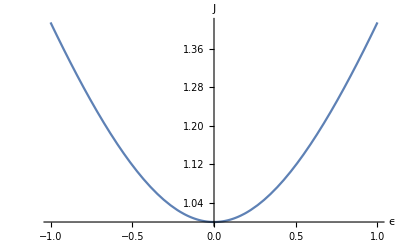

```mathematica
fig = Plot[JAchi,{ϵ,-1,1},AxesLabel->{"ϵ","J"}, PlotRange->Full]
```

```mathematica
Export["jac_Aeps_Achi.pdf",fig]
```

jac_Aeps_Achi.pdf

```mathematica
ellip =Tan[RandomVariate[UniformDistribution[{-Pi/4,Pi/4}],1000000]];
```

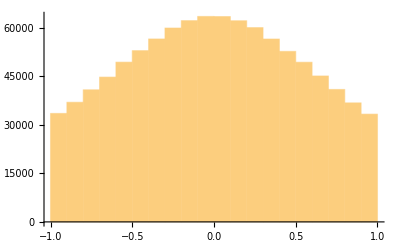

```mathematica
Histogram[ellip]
```

#### Linear quadratures

Since we will be sampling in ((A^+)_x,(A^+)_y,(A^×)_x,(A^×)_y), we want to know what a uniform prior on those quantities implies for (A,ϵ), without really caring about the (θ,ϕ) angles. We want to compute the following Jacobian:
	J = |(∂(A, ϵ, θ, ϕ))/(∂((A^+)_x,(A^+)_y,(A^×)_x,(A^×)_y))|

```mathematica
Axys = {Apx,Apy,Acx,Acy};
```

```mathematica
d=Assuming[Element[Aeps,Reals],FullSimplify[Det[D[Aeps//.AepToAxAy,{Axys}]]]]
```

-(2/(√((Acy+Apx)^2+(Acx-Apy)^2) √((Acy-Apx)^2+(Acx+Apy)^2) (√((Acy+Apx)^2+(Acx-Apy)^2)+√((Acy-Apx)^2+(Acx+Apy)^2))))

```mathematica
J=Assuming[{CL>0,CR>0,A>0,-1<=ϵ<=1},FullSimplify[Abs[d]//.AxAyToCphi//.CphiToAep]]
```

1/(A^3-A^3 ϵ^2)

```mathematica
PowerExpand@Log[J]
```

-Log[A^3-A^3 ϵ^2]

```mathematica
FullSimplify[PowerExpand@Log[-d],Element[Aeps,Reals]]
```

Log[2]-1/2 Log[(Acy+Apx)^2+(Acx-Apy)^2]-1/2 Log[(Acy-Apx)^2+(Acx+Apy)^2]-Log[√((Acy+Apx)^2+(Acx-Apy)^2)+√((Acy-Apx)^2+(Acx+Apy)^2)]

As a sanity check, let’s make sure that we get the right Jacobian in going from ((A^+)_x,(A^+)_y,(A^×)_x,(A^×)_y) to (A^+,A^×,φ^+,φ^×), i.e. J=1/(A^+A^×)

```mathematica
Aphi={Ap,Ac,φp,φc};
```

```mathematica
Assuming[{Ap>0,Ac>0,Element[Aphi,Reals]},FullSimplify[
Abs[Det[D[Aphi//.AphiToAxAy,{Axys}]]]//.AxAyToAphi]]
```

1/(Ac Ap)

Also compute the Jacobian between plus and cross and A ellip

```mathematica
AphiToAep = AphiToAxAy//.AxAyToCphi//.CphiToAep;
AepToAphi = Simplify[AepToCphi//.CphiToAphi];
```

```mathematica
J2=Assuming[{Ap>0,Ac>0, Element[Aphi,Reals]},FullSimplify[
Abs[Det[D[Aeps//.AepToAphi,{Aphi}]]]]]
```

(2 Ac Ap)/(√(Ac^4+Ap^4+2 Ac^2 Ap^2 Cos[2 φc-2 φp]) (√(Ac^2+Ap^2-2 Ac Ap Sin[φc-φp])+√(Ac^2+Ap^2+2 Ac Ap Sin[φc-φp])))

```mathematica
PowerExpand@Log[J2]
```

Log[2]+Log[Ac]+Log[Ap]-1/2 Log[Ac^4+Ap^4+2 Ac^2 Ap^2 Cos[2 φc-2 φp]]-Log[√(Ac^2+Ap^2-2 Ac Ap Sin[φc-φp])+√(Ac^2+Ap^2+2 Ac Ap Sin[φc-φp])]

```mathematica
J2b = FullSimplify[J2//.AphiToAep, Element[Aeps,Reals]&&A>0&&-1<ϵ<1]
```

(√(((1+ϵ^2)^2)/((-1+ϵ^2)^2)-Cos[2 θ]^2))/(2 A)

```mathematica
FortranForm[J2b]
```

Sqrt((1 + ϵ**2)**2/(-1 + ϵ**2)**2 - Cos(2*θ)**2)/(2.*A)

```mathematica
PowerExpand@Log[J2b]
```

-Log[2]-Log[A]+1/2 Log[((1+ϵ^2)^2)/((-1+ϵ^2)^2)-Cos[2 θ]^2]

```mathematica
Assuming[Element[Aphi,Reals]&&Ap>0&&Ac>0,FullSimplify[TrigToExp[Cos[2θ]//.AepToAphi]]]
```

(-Ac^2+Ap^2)/(√(Ac^4+Ap^4+2 Ac^2 Ap^2 Cos[2 φc-2 φp]))

```mathematica
Assuming[Element[Aphi,Reals]&&Ap>0&&Ac>0,FullSimplify[TrigToExp[A//.AepToAphi]]]
```

1/2 (√(Ac^2+Ap^2-2 Ac Ap Sin[φc-φp])+√(Ac^2+Ap^2+2 Ac Ap Sin[φc-φp]))

```mathematica
Assuming[Element[Aphi,Reals]&&Ap>0&&Ac>0,FullSimplify[TrigToExp[ϵ^2//.AepToAphi]]]
```

(Ac^2+Ap^2-√(Ac^4+Ap^4+2 Ac^2 Ap^2 Cos[2 φc-2 φp]))/(Ac^2+Ap^2+√(Ac^4+Ap^4+2 Ac^2 Ap^2 Cos[2 φc-2 φp]))

```mathematica
Assuming[Element[Aphi,Reals]&&Ap>0&&Ac>0&&CL>0&&CR>0,FullSimplify[AphiToAxAy//.AxAyToCphi]]
```

{Ap→√(CL^2+CR^2+2 CL CR Cos[ϕL+ϕR]),Ac→√(CL^2+CR^2-2 CL CR Cos[ϕL+ϕR]),φp→ArcTan[CL Cos[ϕL]+CR Cos[ϕR],-CL Sin[ϕL]+CR Sin[ϕR]],φc→ArcTan[-CL Sin[ϕL]-CR Sin[ϕR],-CL Cos[ϕL]+CR Cos[ϕR]]}

Let’s compute the Jacobian from the circular polarization to the elliptical one:

```mathematica
Cphi={CL,CR,ϕR,ϕL};
```

```mathematica
J3=Assuming[{CL>0,CR>0,A>0,-1<=ϵ<=1},FullSimplify[Abs[Det[D[Aeps//.AepToCphi,{Cphi}]]]]]
```

1/(√2 (CL+CR))

### Plots

#### Animate transformations

```mathematica
xyFromPhase[ϕ_]:={Cos[ϕ],Sin[ϕ]}

xypFromAep[A_,ϵ_,θ_,ϕ_]:={1/2 A (1+ϵ) Cos[θ-ϕ]+1/2 (A-A ϵ) Cos[θ+ϕ],-1/2 A (1+ϵ) Sin[θ-ϕ]+1/2 (A-A ϵ) Sin[θ+ϕ]}
xycFromAep[A_,ϵ_,θ_,ϕ_]:={1/2 A (1+ϵ) Sin[θ-ϕ]+1/2 (A-A ϵ) Sin[θ+ϕ],1/2 A (1+ϵ) Cos[θ-ϕ]-1/2 (A-A ϵ) Cos[θ+ϕ]}
```

```mathematica
w =2.5;
Manipulate[Animate[
Show[
(* Graphics[Circle[{0,-w},1]], *)
Graphics[{Red,Thick,Arrow[{{0,-w},{0,-w}+xypFromAep[1,ϵ,θ,ϕ]}]}],
Graphics[{Red,Arrow[{{0,-w},{xypFromAep[1,ϵ,θ,ϕ][[1]],-w}}]}],
Graphics[{Red,Circle[{0,-w},Norm[xypFromAep[1,ϵ,θ,ϕ]]]}],
Graphics[{Red,Dashed,
Line[{{Norm[xypFromAep[1,ϵ,θ,ϕ]],-w},{Norm[xypFromAep[1,ϵ,θ,ϕ]],0}}],
Line[{{-Norm[xypFromAep[1,ϵ,θ,ϕ]],-w},{-Norm[xypFromAep[1,ϵ,θ,ϕ]],0}}]}],

(* Graphics[Circle[{-w,0},1]],*)
Graphics[{Darker[Green],Thick,Arrow[{{-w,0},{-w,0}+xycFromAep[1,ϵ,θ,ϕ+π/2]}]}],
Graphics[{Darker[Green],Circle[{-w,0},Norm[xycFromAep[1,ϵ,θ,ϕ]]]}],
Graphics[{Darker[Green],Arrow[{{-w,0},{-w,xycFromAep[1,ϵ,θ,ϕ+π/2][[2]]}}]}],
Graphics[{Darker[Green],Dashed,
Line[{{-w,Norm[xycFromAep[1,ϵ,θ,ϕ]]},{0,Norm[xycFromAep[1,ϵ,θ,ϕ]]}}],
Line[{{-w,-Norm[xycFromAep[1,ϵ,θ,ϕ]]},{0,-Norm[xycFromAep[1,ϵ,θ,ϕ]]}}]}],

Graphics[{EdgeForm[{Thickness[0.015],ColorData[97][1]}],White,Rotate[#,θ,{0,0}]&@Ellipsoid[{0,0},{1,Abs[ϵ]}]}],

Graphics[{ColorData[97][1],Thick,Arrow[{{0,0},{Cos[ϕ]Cos[θ]-ϵ Sin[-ϕ]Sin[θ],Cos[ϕ]Sin[θ]+ϵ Sin[-ϕ]Cos[θ]}}]}],

Graphics[{Red,Arrow[{{0,0},{Cos[ϕ]Cos[θ]-ϵ Sin[-ϕ]Sin[θ],0}}]}],
Graphics[{Red,Dotted,
Line[{{Cos[ϕ]Cos[θ]-ϵ Sin[-ϕ]Sin[θ],0},{Cos[ϕ]Cos[θ]-ϵ Sin[-ϕ]Sin[θ],-w}}]
}],

Graphics[{Darker[Green],Arrow[{{0,0},{0,Cos[ϕ]Sin[θ]+ϵ Sin[-ϕ]Cos[θ]}}]}],
Graphics[{Darker[Green],Dotted,
Line[{{0,Cos[ϕ]Sin[θ]+ϵ Sin[-ϕ]Cos[θ]},{-w, Cos[ϕ]Sin[θ]+ϵ Sin[-ϕ]Cos[θ]}}]}]
]
,{ϕ,0,2π}],
{ϵ,-1,1},{θ,0,π}
]
```

```mathematica
AxAyToCphi//.CphiToAep
```

{Apx→1/2 A (1+ϵ) Cos[θ-ϕ]+1/2 (A-A ϵ) Cos[θ+ϕ],Apy→-1/2 A (1+ϵ) Sin[θ-ϕ]+1/2 (A-A ϵ) Sin[θ+ϕ],Acx→1/2 A (1+ϵ) Sin[θ-ϕ]+1/2 (A-A ϵ) Sin[θ+ϕ],Acy→1/2 A (1+ϵ) Cos[θ-ϕ]-1/2 (A-A ϵ) Cos[θ+ϕ]}

```mathematica
Norm[xypFromAep[1,ϵ,θ,ϕ]]
```

√(Abs[1/2 (1+ϵ) Cos[θ-ϕ]+1/2 (1-ϵ) Cos[θ+ϕ]]^2+Abs[-1/2 (1+ϵ) Sin[θ-ϕ]+1/2 (1-ϵ) Sin[θ+ϕ]]^2)

```mathematica
Show[Graphics[Rotate[#,π/4,{0,0}]&@Ellipsoid[{0,0},{1,ϵ}]]]
```

-Graphics-

#### Jacobians

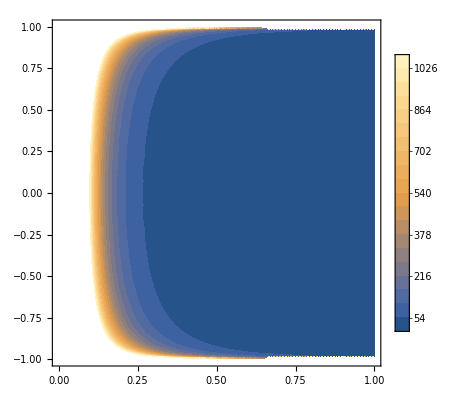

```mathematica
ContourPlot[1/(A^3-A^3 ϵ^2),{A,0,1},{ϵ,-1,1},Contours->20,ContourStyle->None, PlotLegends->Automatic]
```

```mathematica
Plot3D[1/(A^3-A^3 ϵ^2),{A,0,1},{ϵ,-1,1},AxesLabel->{"A","ϵ","J"}]
```

-Graphics3D-

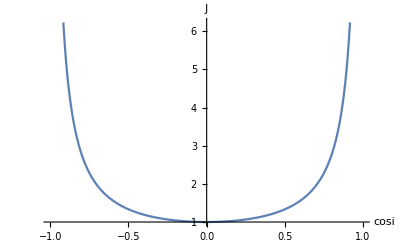

```mathematica
Plot[1/(A^3-A^3 ϵ^2)/.{A->1},{ϵ,-1,1},AxesLabel->{"cosi","J"}]
```

#### Coordinate transformations

```mathematica
Simplify[ϵ//.AepToAxAy]
```

(√((Acy+Apx)^2+(Acx-Apy)^2)-√((Acy-Apx)^2+(Acx+Apy)^2))/(√((Acy+Apx)^2+(Acx-Apy)^2)+√((Acy-Apx)^2+(Acx+Apy)^2))

```mathematica
Simplify[ϵ//.AepToCphi//.CphiToAphi//.{Ap->1,Ac->1}]
```

(-√(1-Sin[φc-φp])+√(1+Sin[φc-φp]))/(√(1-Sin[φc-φp])+√(1+Sin[φc-φp]))

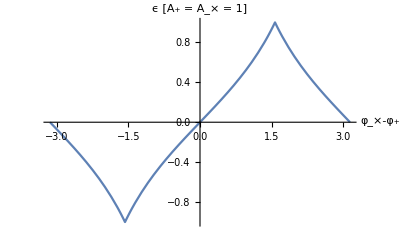

```mathematica
Plot[(-√(1-Sin[φc-φp])+√(1+Sin[φc-φp]))/(√(1-Sin[φc-φp])+√(1+Sin[φc-φp]))/.(φc-φp)->Δφ,{Δφ,-Pi,Pi},AxesLabel->{"φ_×-φ_+","ϵ [A_+ = A_× = 1]"}]
```

```mathematica
FullSimplify[A//.AepToAxAy//.AxAyToAphi,Element[Axys,Reals]]
```

1/2 (√(Ac^2+Ap^2-2 Ac Ap Sin[φc-φp])+√(Ac^2+Ap^2+2 Ac Ap Sin[φc-φp]))

```mathematica
FullSimplify[J-(-3*Log[A]-Log[1-ϵ^2]),A>0&&-1≤ϵ<1]
```

1/(A^3-A^3 ϵ^2)+3 Log[A]+Log[1-ϵ^2]

```mathematica
FullSimplify[{ϕ,θ}//.AepToCphi]
```

{1/2 (-ϕL+ϕR),1/2 (-ϕL-ϕR)}

```mathematica
FullSimplify[{ϕR,ϕL}//.CphiToAxAy]
```

{ArcTan[Acy+Apx,-Acx+Apy],ArcTan[-Acy+Apx,-Acx-Apy]}

```mathematica
FullSimplify[FullSimplify[A//.AepToCphi//.CphiToAphi//.{φp->ϕ,φc->ϕ-Pi/2}]//.{Ap->(1+cosi^2)A,Ac->2 cosi A},A>0&&-1<cosi<1]
```

A (1+cosi^2)

```mathematica
FullSimplify[FullSimplify[ϵ//.AepToCphi//.CphiToAphi//.{φp->ϕ,φc->ϕ-Pi/2}]//.{Ap->(1+cosi^2)A,Ac->2 cosi A},A>0&&-1<cosi<1]
```

-(2 cosi)/(1+cosi^2)

```mathematica
Solve[ϵ==-(2 cosi)/(1+cosi^2), cosi]
```

{{cosi→(-1-√(1-ϵ^2))/ϵ},{cosi→(-1+√(1-ϵ^2))/ϵ}}

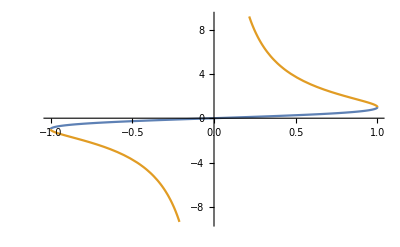

```mathematica
Plot[{(1-√(1-ϵ^2))/ϵ,(1+√(1-ϵ^2))/ϵ},{ϵ,-1,1}]
```

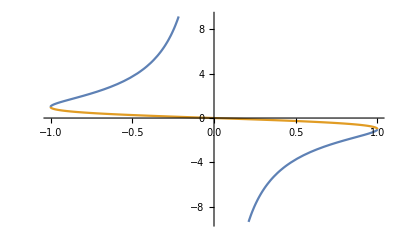

```mathematica
Plot[{(-1-√(1-ϵ^2))/ϵ,(-1+√(1-ϵ^2))/ϵ},{ϵ,-1,1}]
```

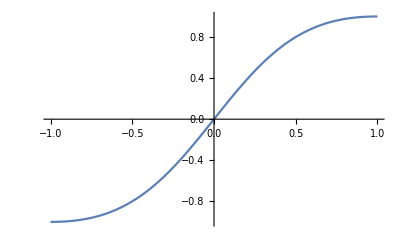

```mathematica
Plot[(2 cosi)/(1+cosi^2),{cosi,-1,1}]
```

```mathematica
Jcosi = FullSimplify[Abs[D[(-1+√(1-ϵ^2))/ϵ,ϵ]],-1<ϵ<1]
```

(-1+1/(√(1-ϵ^2)))/ϵ^2

```mathematica
ϵ^2//.AepToAxAy
```

((1/2 √((Acy+Apx)^2+(Acx-Apy)^2)-1/2 √((Acy-Apx)^2+(Acx+Apy)^2))^2)/((1/2 √((Acy+Apx)^2+(Acx-Apy)^2)+1/2 √((Acy-Apx)^2+(Acx+Apy)^2))^2)

```mathematica
FullSimplify[Jcosi //. ϵ->(2 cosi)/(1+cosi^2),-1<cosi<1]
```

-((1+cosi^2)^2)/(2 (-1+cosi^2))

```mathematica
PowerExpand@Log[Jcosi]
```

-2 Log[ϵ]+Log[-1+1/(√(1-ϵ^2))]

```mathematica
FullSimplify[Abs[D[(1-√(1-ϵ^2))/ϵ,ϵ]],-1<ϵ<1]
```

(-1+1/(√(1-ϵ^2)))/ϵ^2

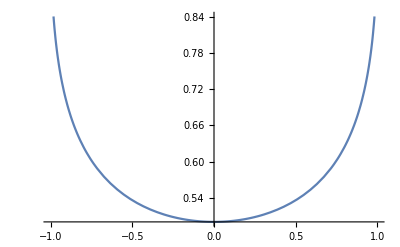

```mathematica
Plot[Abs[(-1+√(1-ϵ^2))/ϵ^2],{ϵ,-1,1}]
```

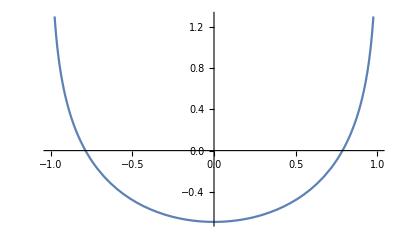

```mathematica
Plot[-2 Log[Abs[ϵ]]+Log[Abs[-1+1/(√(1-ϵ^2))]],{ϵ,-1,1}]
```

```mathematica
FullSimplify[Abs[(-1+√(1-ϵ^2))/ϵ^2], -1<ϵ<1]
```

1/(1+√(1-ϵ^2))

```mathematica
Log[-1/ϵ^2]
```

Log[-1/ϵ^2]

```mathematica
FortranForm[FullSimplify[ϕ//.AepToAxAy]]
```

(-ArcTan(-Acy + Apx,-Acx - Apy) + ArcTan(Acy + Apx,-Acx + Apy))/2.